## 2.131 Advanced Instrumentation and Measurement Lecture 2 Assignment

#### Ariel Mobius, 5 February 2026

We make some 3 axis acceleration measurements using the TinkerForge Accelerometer Bricklet  or the TinkerForge IMU Brick (or Bricklet) connected to the Master Brick using the Logger functionality in the Brick Viewer as shown in class.

#### Import .CSV file from TinkerForge Brick Viewer Logger

When you set up the Logger in the Brick Viewer save the filename. Replace the following with your file name:

```mathematica
file="\Users\ariel\Downloads\IMU.csv";
```

Note that you will need to change the file name in the Logger for each repeated measurement you make (it does not seem to overwrite existing files).

Now we can import the CSV data using  the function Import[].

```mathematica
Import[file];
```

You can suppress the output by including a ; at the end of the line.

Note that TinkerForge stores the logged data using “;” as delimiters. We want them to be converted to “,”. The following achieves what we want:

```mathematica
data=Import[file,"Table","FieldSeparators"->";"];
```

We can access the first row (the header information for the columns) using

```mathematica
data[[1]]
```

{TIME,NAME,UID,VAR,RAW,UNIT}

and the first row containing the x-axis acceleration:

```mathematica
data[[2]]
```

{02/05/2026 13:30:46,Accelerometer Bricklet 2.0,HC9,Acceleration-X,9939,g/10000}

and the value, x1, of this acceleration as (we change it to a real number):

```mathematica
x1=N[data[[2]][[5]]]
```

9939.

```mathematica
x1
```

9939.

This is in units of 1/10000 m/s^2 so to convert to m/s^2 we do:

```mathematica
x1=x1/10000.
```

0.9939

We need to separate the x,y and z accelerations. We do this as follows:

```mathematica
n=Length[data]
```

2539

```mathematica
x=data[[2;;n]][[5]]
```

{02/05/2026 13:30:46,Accelerometer Bricklet 2.0,HC9,Acceleration-Y,5598,g/10000}

```mathematica
a=data[[1;;4]]
```

{{TIME,NAME,UID,VAR,RAW,UNIT},{02/05/2026 13:30:46,Accelerometer Bricklet 2.0,HC9,Acceleration-X,9939,g/10000},{02/05/2026 13:30:46,Accelerometer Bricklet 2.0,HC9,Acceleration-Y,5598,g/10000},{02/05/2026 13:30:46,Accelerometer Bricklet 2.0,HC9,Acceleration-Z,3327,g/10000}}

```mathematica
a[[2]][[5]]
```

9939

#### Extract the x, y and z accelerations (and convert to m/s^2)

```mathematica
x=Table[0.0,(n-1)/3];  (* note that the number of x values is (n-1)/3 *)
y=Table[0.0,(n-1)/3];  (* note that the number of x values is (n-1)/3 *)
z=Table[0.0,(n-1)/3];  (* note that the number of x values is (n-1)/3 *)
a=0.0001; (* conversion factor to m/s^2 *)
i=1;
Do[
x[[i]]=a data[[j]][[5]];
y[[i]]=a data[[j+1]][[5]];
z[[i]]=a data[[j+2]][[5]];
i=i+1,
{j,2,n,3}]
```

```mathematica
%17
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

#### Plot the Data

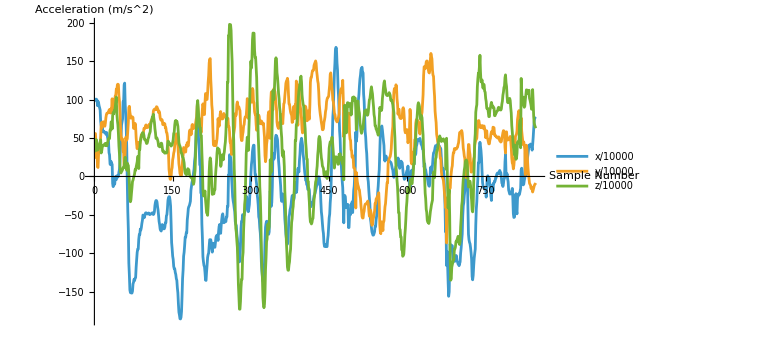

```mathematica
ListLinePlot[{x,y,z},PlotLegends->{"x","y","z"},AxesLabel->{"Sample Number","Acceleration (m/s^2)"},ImageSize->Large]
```

Note that if you hold the accelerometer horizontal, the mean value of the z axis acceleration will be the measured acceleration of gravity (i.e., around 9.8 m/s^2) .

```mathematica
Mean[z]
```

34.7838

If we want the similar colors as are displayed in the Brick Viewer then we use:

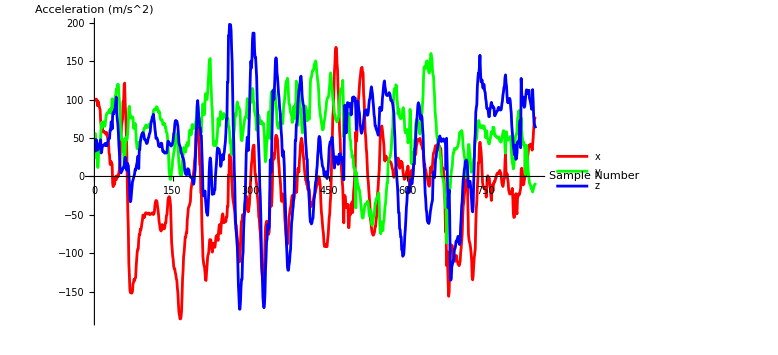

```mathematica
ListLinePlot[{x,y,z},PlotLegends->{"x","y","z"},PlotStyle->{Red,Green,Blue},AxesLabel->{"Sample Number","Acceleration (m/s^2)"},ImageSize->Large]
```

#### Generate Time Axis

We sampled every 10 ms (100 Hz sampling rate). So lets define the sampling increment as:

```mathematica
Δt=0.01;
```

So we can generate a signal, t, representing the time:

```mathematica
t=Range[Δt,Δt(n-1)/3,Δt];
```

Check that t and z  have the same lengths:

```mathematica
Length[t]
```

846

```mathematica
Length[z]
```

846

#### Plot the z-axis Acceleration Signal

Note that we have to transpose {t,z}:

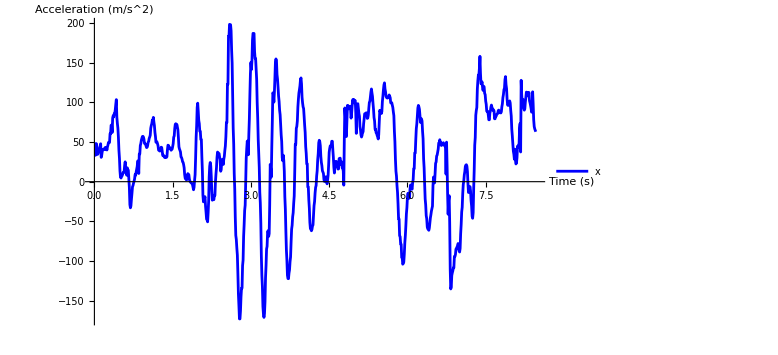

```mathematica
ListLinePlot[Transpose[{t,z}],PlotLegends->{"x","y","z"},PlotStyle->{Red,Green,Blue},AxesLabel->{"Time (s)","Acceleration (m/s^2)"},ImageSize->Large]
```